```mathematica
ClearAll["Global`*"]
```

```mathematica
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
D2a[n_,k_]:=D2a[n,k]=Sum[D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1
DD[n_,z_]:=DD[n,z]=Sum[FactorialPower[z,a]/a! D2a[n,a],{a,0,Log[2,n]}]
EE[n_,z_,b_]:=EE[n,z,b]=Sum[FactorialPower[z,a]/a! E2a[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
D1b[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1b[n/b^j,k,b],{j,0,Log[b,n]}]
E1b[n_,k_,b_]:=Sum[FactorialPower[k,a]/a! E2b[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
E2b[n_,k_, a_]:= E2b[n,k,a]=Sum[ E2b[n/j,k-1,a],{j,2,n}]-a Sum[ E2b[n/(a j),k-1,a],{j,1,n/a}];E2b[n_,0,a_]:=1
D1c[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
D1d[n_, z_, b_] := Sum[ 
Binomial[z+j-1,z-1]  Binomial[z,k]b^j  E2[n/b^j,k,b],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]
D1e[n_, k_, b_] := Grid[Table[ 
Binomial[k+j-1,k-1]  Binomial[k,a]b^j  E2[n/b^j,a,b],{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]]
D1e2[n_, k_, b_] := Grid[Table[ 
Binomial[k+j-1,k-1]  FactorialPower[k,a]/a!b^j  E2[n/b^j,a,b]/k,{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]]
D1c2[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
lin[n_,b_]:=Sum[(-1)^(k+1)/k E2b[n,k,b],{k,1,Log[2,n]}]
M2[n_,a_]:=Sum[(-1)^k( E2b[n,k,a]-a E2b[n/a,k,a]),{k,0,Log[a,n]}]
```

```mathematica
M2[30,1.1]
```

-3.

```mathematica
D1c[30,-1,1.1]
```

-3.

```mathematica
(D1c2[100,.0000001,2]-1)/.0000001
```

28.5333

```mathematica
lin[100,2]
```

4/5

```mathematica
D1e2[100,.0000001,2]
```

1.×10^7 E2[100,0,2] | 1. E2[100,1,2] | -0.5 E2[100,2,2] | 0.333333 E2[100,3,2] | -0.25 E2[100,4,2] | 0.2 E2[100,5,2] | -0.166667 E2[100,6,2]
2. E2[50,0,2] | 2.×10^-7 E2[50,1,2] | -1.×10^-7 E2[50,2,2] | 6.66667×10^-8 E2[50,3,2] | -5.×10^-8 E2[50,4,2] | 4.×10^-8 E2[50,5,2] | 
2. E2[25,0,2] | 2.×10^-7 E2[25,1,2] | -1.×10^-7 E2[25,2,2] | 6.66667×10^-8 E2[25,3,2] | -5.×10^-8 E2[25,4,2] |  | 
2.66667 E2[25/2,0,2] | 2.66667×10^-7 E2[25/2,1,2] | -1.33333×10^-7 E2[25/2,2,2] | 8.88889×10^-8 E2[25/2,3,2] |  |  | 
4. E2[25/4,0,2] | 4.×10^-7 E2[25/4,1,2] | -2.×10^-7 E2[25/4,2,2] |  |  |  | 
6.4 E2[25/8,0,2] | 6.4×10^-7 E2[25/8,1,2] |  |  |  |  | 
10.6667 E2[25/16,0,2] |  |  |  |  |  |

```mathematica
D1e[100,-1,2]
```

E2[100,0,2] | -E2[100,1,2] | E2[100,2,2] | -E2[100,3,2] | E2[100,4,2] | -E2[100,5,2] | E2[100,6,2]
-2 E2[50,0,2] | 2 E2[50,1,2] | -2 E2[50,2,2] | 2 E2[50,3,2] | -2 E2[50,4,2] | 2 E2[50,5,2] | 
0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 |  |  |  | 
0 | 0 |  |  |  |  | 
0 |  |  |  |  |  |

```mathematica
D1e[900,1,2]
```

E2[900,0,2] | E2[900,1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 E2[450,0,2] | 2 E2[450,1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
4 E2[225,0,2] | 4 E2[225,1,2] | 0 | 0 | 0 | 0 | 0 | 0 |  | 
8 E2[225/2,0,2] | 8 E2[225/2,1,2] | 0 | 0 | 0 | 0 | 0 |  |  | 
16 E2[225/4,0,2] | 16 E2[225/4,1,2] | 0 | 0 | 0 | 0 |  |  |  | 
32 E2[225/8,0,2] | 32 E2[225/8,1,2] | 0 | 0 | 0 |  |  |  |  | 
64 E2[225/16,0,2] | 64 E2[225/16,1,2] | 0 | 0 |  |  |  |  |  | 
128 E2[225/32,0,2] | 128 E2[225/32,1,2] | 0 |  |  |  |  |  |  | 
256 E2[225/64,0,2] | 256 E2[225/64,1,2] |  |  |  |  |  |  |  | 
512 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,2,2]
```

E2[900,0,2] | 2 E2[900,1,2] | E2[900,2,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 E2[450,0,2] | 8 E2[450,1,2] | 4 E2[450,2,2] | 0 | 0 | 0 | 0 | 0 | 0 | 
12 E2[225,0,2] | 24 E2[225,1,2] | 12 E2[225,2,2] | 0 | 0 | 0 | 0 | 0 |  | 
32 E2[225/2,0,2] | 64 E2[225/2,1,2] | 32 E2[225/2,2,2] | 0 | 0 | 0 | 0 |  |  | 
80 E2[225/4,0,2] | 160 E2[225/4,1,2] | 80 E2[225/4,2,2] | 0 | 0 | 0 |  |  |  | 
192 E2[225/8,0,2] | 384 E2[225/8,1,2] | 192 E2[225/8,2,2] | 0 | 0 |  |  |  |  | 
448 E2[225/16,0,2] | 896 E2[225/16,1,2] | 448 E2[225/16,2,2] | 0 |  |  |  |  |  | 
1024 E2[225/32,0,2] | 2048 E2[225/32,1,2] | 1024 E2[225/32,2,2] |  |  |  |  |  |  | 
2304 E2[225/64,0,2] | 4608 E2[225/64,1,2] |  |  |  |  |  |  |  | 
5120 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
DD[100,-1]
```

1

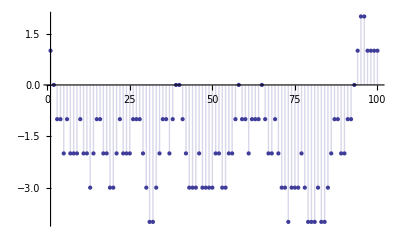

```mathematica
DiscretePlot[ DD[n,-1],{n,1,100}]
```

```mathematica
DiscretePlot[ EE[n,-1,200],{n,1,100}]
```

-Graphics-

```mathematica
Animate[DiscretePlot[ EE[n,7,z],{n,1,100}],{z,2,100}]
```

```mathematica
Animate[DiscretePlot[ EE[n,-1,z],{n,1,100}],{z,2,100}]
```

```mathematica
Animate[DiscretePlot[( EE[n,.0001,z]-1)/.0001,{n,1,100}],{z,2,100}]
```

```mathematica
D1d[1000,-3/2,2]
```

143/128 E2[125/64,0,2]+99/128 E2[125/32,0,2]-297/256 E2[125/32,1,2]+9/16 E2[125/16,0,2]-27/32 E2[125/16,1,2]+135/128 E2[125/16,2,2]+7/16 E2[125/8,0,2]-21/32 E2[125/8,1,2]+105/128 E2[125/8,2,2]-245/256 E2[125/8,3,2]+3/8 E2[125/4,0,2]-9/16 E2[125/4,1,2]+45/64 E2[125/4,2,2]-105/128 E2[125/4,3,2]+(945 E2[125/4,4,2])/1024+3/8 E2[125/2,0,2]-9/16 E2[125/2,1,2]+45/64 E2[125/2,2,2]-105/128 E2[125/2,3,2]+(945 E2[125/2,4,2])/1024-(2079 E2[125/2,5,2])/2048+1/2 E2[125,0,2]-3/4 E2[125,1,2]+15/16 E2[125,2,2]-35/32 E2[125,3,2]+315/256 E2[125,4,2]-693/512 E2[125,5,2]+(3003 E2[125,6,2])/2048+3/2 E2[250,0,2]-9/4 E2[250,1,2]+45/16 E2[250,2,2]-105/32 E2[250,3,2]+945/256 E2[250,4,2]-2079/512 E2[250,5,2]+(9009 E2[250,6,2])/2048-(19305 E2[250,7,2])/4096-3 E2[500,0,2]+9/2 E2[500,1,2]-45/8 E2[500,2,2]+105/16 E2[500,3,2]-945/128 E2[500,4,2]+2079/256 E2[500,5,2]-(9009 E2[500,6,2])/1024+(19305 E2[500,7,2])/2048-(328185 E2[500,8,2])/32768+E2[1000,0,2]-3/2 E2[1000,1,2]+15/8 E2[1000,2,2]-35/16 E2[1000,3,2]+315/128 E2[1000,4,2]-693/256 E2[1000,5,2]+(3003 E2[1000,6,2])/1024-(6435 E2[1000,7,2])/2048+(109395 E2[1000,8,2])/32768-(230945 E2[1000,9,2])/65536

```mathematica
D1e[900,-1,2]
```

E2[900,0,2] | -E2[900,1,2] | E2[900,2,2] | -E2[900,3,2] | E2[900,4,2] | -E2[900,5,2] | E2[900,6,2] | -E2[900,7,2] | E2[900,8,2] | -E2[900,9,2]
-2 E2[450,0,2] | 2 E2[450,1,2] | -2 E2[450,2,2] | 2 E2[450,3,2] | -2 E2[450,4,2] | 2 E2[450,5,2] | -2 E2[450,6,2] | 2 E2[450,7,2] | -2 E2[450,8,2] | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 | 0 | 0 | 0 |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |

```mathematica
D1f[n_, k_, b_] := Sum[ 
Binomial[k+j-1,k-1]  Binomial[k,a]b^j  E2a[n/b^j,a,b],{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]
```

```mathematica
ME2[n_,b_]:=Sum[ (-1)^k E2a[n,k,b],{k,0,Log[If[b<2,b,2],n]}]
ME2a[n_,b_]:=ME2[n,b]-b ME2[n/b,b]
ME2b[n_,a_]:=Sum[ (-1)^k (E2a[n,k,a]-a E2a[n/a,k,a]),{k,0,Log[If[a<2,a,2],n]}]
```

```mathematica
ME2[100,2]
```

-13

```mathematica
M2[n_, a_] := Sum[ (-1)^k (k+1)(E2a[n,k,a]-2a E2a[n/a,k,a]+a^2 E2a[n/(a^2),k,a]),{k,0,Log[If[a<2,a,2],n]}]
```

```mathematica
M2[100,4]
```

19

```mathematica
DD[100,-2]
```

19

```mathematica
D1c[100,-2,2]
```

19

```mathematica
D1e[2400,-2,3]
```

E2[2400,0,3] | -2 E2[2400,1,3] | 3 E2[2400,2,3] | -4 E2[2400,3,3] | 5 E2[2400,4,3] | -6 E2[2400,5,3] | 7 E2[2400,6,3] | -8 E2[2400,7,3] | 9 E2[2400,8,3] | -10 E2[2400,9,3] | 11 E2[2400,10,3] | -12 E2[2400,11,3]
-6 E2[800,0,3] | 12 E2[800,1,3] | -18 E2[800,2,3] | 24 E2[800,3,3] | -30 E2[800,4,3] | 36 E2[800,5,3] | -42 E2[800,6,3] | 48 E2[800,7,3] | -54 E2[800,8,3] | 60 E2[800,9,3] |  | 
9 E2[800/3,0,3] | -18 E2[800/3,1,3] | 27 E2[800/3,2,3] | -36 E2[800/3,3,3] | 45 E2[800/3,4,3] | -54 E2[800/3,5,3] | 63 E2[800/3,6,3] | -72 E2[800/3,7,3] | 81 E2[800/3,8,3] |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |  |  |

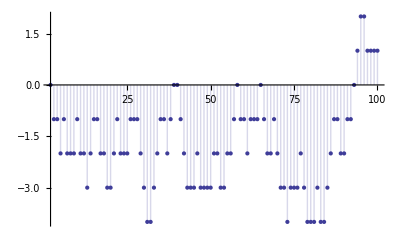

```mathematica
DiscretePlot[ME2b[n,2],{n,2,100}]
```

```mathematica
DiscretePlot[D1f[n,-1,2],{n,2,100}]
```

-Graphics-

```mathematica
DiscretePlot[ME2[n,(3/2)]-(3/2)ME2[n/(3/2),(3/2)],{n,2,100}]
```

-Graphics-

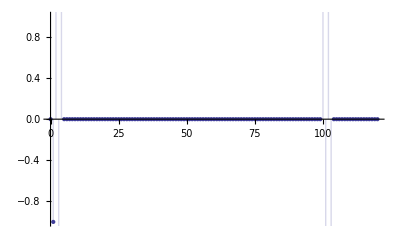

```mathematica
DiscretePlot[(-1)^k (E2a[100,k,1.0001]-1.0001 E2a[100/1.0001,k,1.0001]),{k,0,120},PlotRange->{{0,120},{-1,1}}]
```

```mathematica
D1e[2400,-2,7]
```

E2[2400,0,7] | -2 E2[2400,1,7] | 3 E2[2400,2,7] | -4 E2[2400,3,7] | 5 E2[2400,4,7] | -6 E2[2400,5,7] | 7 E2[2400,6,7] | -8 E2[2400,7,7] | 9 E2[2400,8,7] | -10 E2[2400,9,7] | 11 E2[2400,10,7] | -12 E2[2400,11,7]
-14 E2[2400/7,0,7] | 28 E2[2400/7,1,7] | -42 E2[2400/7,2,7] | 56 E2[2400/7,3,7] | -70 E2[2400/7,4,7] | 84 E2[2400/7,5,7] | -98 E2[2400/7,6,7] | 112 E2[2400/7,7,7] | -126 E2[2400/7,8,7] |  |  | 
49 E2[2400/49,0,7] | -98 E2[2400/49,1,7] | 147 E2[2400/49,2,7] | -196 E2[2400/49,3,7] | 245 E2[2400/49,4,7] | -294 E2[2400/49,5,7] |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  |  |  |

```mathematica
D1e[1200,-3,2]
```

E2[1200,0,2] | -3 E2[1200,1,2] | 6 E2[1200,2,2] | -10 E2[1200,3,2] | 15 E2[1200,4,2] | -21 E2[1200,5,2] | 28 E2[1200,6,2] | -36 E2[1200,7,2] | 45 E2[1200,8,2] | -55 E2[1200,9,2] | 66 E2[1200,10,2]
-6 E2[600,0,2] | 18 E2[600,1,2] | -36 E2[600,2,2] | 60 E2[600,3,2] | -90 E2[600,4,2] | 126 E2[600,5,2] | -168 E2[600,6,2] | 216 E2[600,7,2] | -270 E2[600,8,2] | 330 E2[600,9,2] | 
12 E2[300,0,2] | -36 E2[300,1,2] | 72 E2[300,2,2] | -120 E2[300,3,2] | 180 E2[300,4,2] | -252 E2[300,5,2] | 336 E2[300,6,2] | -432 E2[300,7,2] | 540 E2[300,8,2] |  | 
-8 E2[150,0,2] | 24 E2[150,1,2] | -48 E2[150,2,2] | 80 E2[150,3,2] | -120 E2[150,4,2] | 168 E2[150,5,2] | -224 E2[150,6,2] | 288 E2[150,7,2] |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |  |

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
Table[{1.0001^k,(-1)^k (E2a[100,k,1.0001]-1.0001 E2a[100/1.0001,k,1.0001])},{k,0,200}]//TableForm
```

1. | -0.0001
1.0001 | -1.0001
1.0002 | 6.9999
1.0003 | -12.0001
1.0004 | 5.9999
1.0005 | -0.000104955
1.0006 | -0.000105947
1.0007 | -0.00010694
1.0008 | -0.000107933
1.0009 | -0.000108927
1.001 | -0.000109921
1.0011 | -0.000110916
1.0012 | -0.000111911
1.0013 | -0.000112907
1.0014 | -0.000113903
1.0015 | -0.0001149
1.0016 | -0.000115897
1.0017 | -0.000116894
1.0018 | -0.000117892
1.0019 | -0.000118891
1.002 | -0.00011989
1.0021 | -0.00012089
1.0022 | -0.000121889
1.0023 | -0.00012289
1.0024 | -0.000123891
1.0025 | -0.000124892
1.0026 | -0.000125894
1.0027 | -0.000126896
1.0028 | -0.000127899
1.0029 | -0.000128903
1.003 | -0.000129906
1.0031 | -0.000130911
1.0032 | -0.000131915
1.00331 | -0.000132921
1.00341 | -0.000133926
1.00351 | -0.000134932
1.00361 | -0.000135939
1.00371 | -0.000136946
1.00381 | -0.000137954
1.00391 | -0.000138962
1.00401 | -0.00013997
1.00411 | -0.000140979
1.00421 | -0.000141989
1.00431 | -0.000142999
1.00441 | -0.000144009
1.00451 | -0.00014502
1.00461 | -0.000146032
1.00471 | -0.000147044
1.00481 | -0.000148056
1.00491 | -0.000149069
1.00501 | -0.000150082
1.00511 | -0.000151096
1.00521 | -0.00015211
1.00531 | -0.000153125
1.00541 | -0.00015414
1.00551 | -0.000155156
1.00562 | -0.000156172
1.00572 | -0.000157189
1.00582 | -0.000158206
1.00592 | -0.000159224
1.00602 | -0.000160242
1.00612 | -0.000161261
1.00622 | -0.00016228
1.00632 | -0.000163299
1.00642 | -0.00016432
1.00652 | -0.00016534
1.00662 | -0.000166361
1.00672 | -0.000167383
1.00682 | -0.000168405
1.00692 | -0.000169427
1.00702 | -0.00017045
1.00712 | -0.000171474
1.00723 | -0.000172498
1.00733 | -0.000173522
1.00743 | -0.000174547
1.00753 | -0.000175572
1.00763 | -0.000176598
1.00773 | -0.000177625
1.00783 | -0.000178651
1.00793 | -0.000179679
1.00803 | -0.000180707
1.00813 | -0.000181735
1.00823 | -0.000182764
1.00833 | -0.000183793
1.00843 | -0.000184823
1.00854 | -0.000185853
1.00864 | -0.000186884
1.00874 | -0.000187915
1.00884 | -0.000188946
1.00894 | -0.000189979
1.00904 | -0.000191011
1.00914 | -0.000192044
1.00924 | -0.000193078
1.00934 | -0.000194112
1.00944 | -0.000195147
1.00954 | -0.000196182
1.00965 | -0.000197217
1.00975 | -0.000198254
1.00985 | -0.00019929
1.00995 | -0.000200327
1.01005 | 510126.

```mathematica
N[Table[{k,(-1)^k (E2a[1000,k,ss=2]-ss E2a[1000/ss,k,ss])},{k,0,20}]//TableForm]
```

0. | -1.
1. | -1.
2. | -4.
3. | 13.
4. | 98.
5. | -120.
6. | 26.
7. | 20.
8. | -21.
9. | -8.
10. | 0.
11. | 0.
12. | 0.
13. | 0.
14. | 0.
15. | 0.
16. | 0.
17. | 0.
18. | 0.
19. | 0.
20. | 0.

```mathematica
N[Table[{k,(-1)^k (E2a[10000,k,ss=2]-ss E2a[1000/ss,k,ss])},{k,0,20}]//TableForm]
```

0. | -1.
1. | -1.
2. | 7.
3. | 0.
4. | 525.
5. | -1069.
6. | -792.
7. | 1293.
8. | -154.
9. | 1018.
10. | 939.
11. | 320.
12. | 67.
13. | 1.
14. | 0.
15. | 0.
16. | 0.
17. | 0.
18. | 0.
19. | 0.
20. | 0.

```mathematica
Binomial[z,0]
```

1

```mathematica
Limit[ Sum[ Binomial[z+j-1, z-1]a^j,{j,0,Log[a,n]}]/.z->1,a->1]
```

DirectedInfinity[-1+n]

```mathematica
D1e[100,-3,2]
```

E2[100,0,2] | -3 E2[100,1,2] | 6 E2[100,2,2] | -10 E2[100,3,2] | 15 E2[100,4,2] | -21 E2[100,5,2] | 28 E2[100,6,2]
-6 E2[50,0,2] | 18 E2[50,1,2] | -36 E2[50,2,2] | 60 E2[50,3,2] | -90 E2[50,4,2] | 126 E2[50,5,2] | 
12 E2[25,0,2] | -36 E2[25,1,2] | 72 E2[25,2,2] | -120 E2[25,3,2] | 180 E2[25,4,2] |  | 
-8 E2[25/2,0,2] | 24 E2[25/2,1,2] | -48 E2[25/2,2,2] | 80 E2[25/2,3,2] |  |  | 
0 | 0 | 0 |  |  |  | 
0 | 0 |  |  |  |  | 
0 |  |  |  |  |  |

```mathematica
$RecursionLimit=1000000
dr[n_,k_,b_]:=DiscretePlot[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
```

1000000

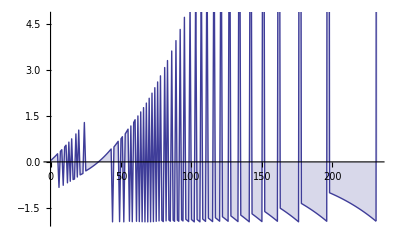

```mathematica
dr[100,1,1.02]
```

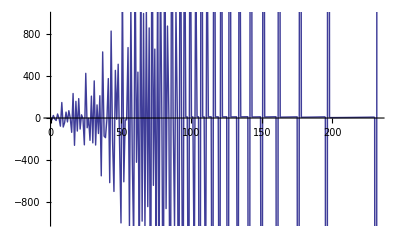

```mathematica
dr[100,2,1.02]
```

```mathematica
Dr2[n_, k_, b_] := DiscretePlot[Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,s,s}],{j,0,Log[b,n]}],{s,0,Log[b,n]},PlotRange->{{0,100},{-.1,.1}}]
```

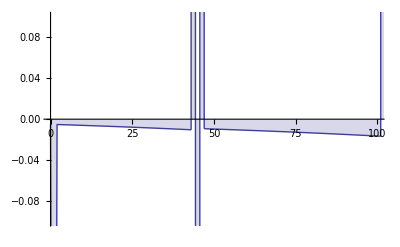

```mathematica
Dr2[5,-1,1.005]
```

```mathematica
Dr3[n_, k_, b_] := Table[{b^s,Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,s,s}],{j,0,Log[b,n]}]},{s,0,Log[b,n]}]//TableForm
```

```mathematica
Dr3[12,-1,1.02]
```

1. | -0.02
1.02 | -1.0244
1.0404 | 3.97097
1.06121 | -3.0339
1.08243 | 4.3773
1.10408 | -5.45441
1.12616 | -0.0474139
1.14869 | -0.052843
1.17166 | -0.0585433
1.19509 | 98.674
1.21899 | -229.242
1.24337 | 131.389
1.26824 | -0.0770143
1.29361 | -0.083342
1.31948 | 141.226
1.34587 | -299.687
1.37279 | 158.243
1.40024 | -0.100815
1.42825 | -0.107714
1.45681 | -0.114909
1.48595 | 2334.
1.51567 | -7298.94
1.54598 | 7596.34
1.5769 | -2631.74
1.60844 | -0.133239
1.64061 | -0.140672
1.67342 | -0.148388
1.70689 | 46.8513
1.74102 | -47.9384
1.77584 | -0.153128
1.81136 | -0.160954
1.84759 | -0.169075
1.88454 | -0.177499
1.92223 | -0.186237
1.96068 | -0.195299
1.99989 | 2498.66
2.03989 | -5161.29
2.08069 | 2663.68
2.1223 | -0.180424
2.16474 | -0.188061
2.20804 | -0.195948
2.2522 | -0.204092
2.29724 | -0.212502
2.34319 | -0.221184
2.39005 | 107.035
2.43785 | -107.749
2.48661 | -0.204091
2.53634 | -0.212054
2.58707 | -0.220274
2.63881 | -0.228758
2.69159 | -0.237514
2.74542 | -0.246549
2.80033 | -0.255873
2.85633 | -0.265493
2.91346 | -0.275418
2.97173 | 4667.71
3.03117 | -9409.28
3.09179 | 4742.68
3.15362 | -0.206531
3.2167 | -0.213185
3.28103 | -0.220022
3.34665 | -0.227047
3.41358 | -0.234266
3.48186 | -0.241682
3.55149 | -0.249301
3.62252 | -0.257128
3.69497 | -0.265169
3.76887 | -0.273428
3.84425 | -0.281912
3.92114 | -0.290625
3.99956 | 285.269
4.07955 | -284.164
4.16114 | -0.200714
4.24436 | -0.206393
4.32925 | -0.212218
4.41584 | -0.218194
4.50415 | -0.224324
4.59424 | -0.230613
4.68612 | -0.237063
4.77984 | -0.243678
4.87544 | -0.250464
4.97295 | -0.257423
5.07241 | -0.264561
5.17386 | -0.271881
5.27733 | -0.279388
5.38288 | -0.287087
5.49054 | -0.294982
5.60035 | -0.303078
5.71235 | -0.311379
5.8266 | -0.319892
5.94313 | 545.251
6.062 | -540.946
6.18324 | -0.123665
6.3069 | -0.126138
6.43304 | -0.128661
6.5617 | -0.131234
6.69293 | -0.133859
6.82679 | -0.136536
6.96333 | -0.139267
7.10259 | -0.142052
7.24465 | -0.144893
7.38954 | -0.147791
7.53733 | -0.150747
7.68808 | -0.153762
7.84184 | -0.156837
7.99867 | -0.159973
8.15865 | -0.163173
8.32182 | -0.166436
8.48826 | -0.169765
8.65802 | -0.17316
8.83118 | -0.176624
9.00781 | -0.180156
9.18796 | -0.183759
9.37172 | -0.187434
9.55916 | -0.191183
9.75034 | -0.195007
9.94535 | -0.198907
10.1443 | -0.202885
10.3471 | -0.206943
10.5541 | -0.211082
10.7652 | -0.215303
10.9805 | -0.219609
11.2001 | -0.224002
11.4241 | -0.228482
11.6526 | -0.233051
11.8856 | 11.8856

```mathematica
DD[5,-1]
```

-2

```mathematica
DD[6,-1]
```

-1

```mathematica
$RecursionLimit=10000
```

10000

```mathematica
Table[{k,(-1)^k( E2b[5,k,1.01]-1.01 E2b[5/1.01,k,1.01]),(-1)^(k+1)/k E2b[5,k,1.01] },{k,1,Log[1.01,5]+10}]//TableForm
```

1 | -1.0104 | -0.04
2 | -0.010808 | -0.5404
3 | -0.0112241 | -0.374138
4 | -0.0116485 | -0.291213
5 | -0.0120813 | -0.241626
6 | -0.0125226 | -0.20871
7 | -0.0129726 | -0.185323
8 | -0.0134314 | -0.167893
9 | -0.0138992 | -0.154435
10 | -0.014376 | -0.14376
11 | -0.0148621 | -0.13511
12 | -0.0153576 | -0.12798
13 | -0.0158626 | -0.12202
14 | -0.0163773 | -0.116981
15 | -0.0169018 | -0.112679
16 | -0.0174364 | -0.108977
17 | -0.0179811 | -0.105771
18 | -0.0185361 | -0.102978
19 | -0.0191016 | -0.100535
20 | -0.0196778 | -0.0983891
21 | -0.0202648 | -0.0964991
22 | 318.041 | -0.094831
23 | -661.591 | 14.9926
24 | 343.523 | -14.3923
25 | -0.019173 | -0.076692
26 | -0.0196212 | -0.0754662
27 | -0.0200765 | -0.0743573
28 | -0.0205389 | -0.0733531
29 | -0.0210085 | -0.0724432
30 | -0.0214855 | -0.0716184
31 | -0.0219699 | -0.0708708
32 | -0.0224619 | -0.0701934
33 | -0.0229615 | -0.0695803
34 | -0.0234689 | -0.0690261
35 | -0.0239841 | -0.0685259
36 | -0.0245072 | -0.0680756
37 | -0.0250385 | -0.0676715
38 | -0.0255779 | -0.0673101
39 | -0.0261255 | -0.0669886
40 | -0.0266816 | -0.066704
41 | -0.0272462 | -0.0664542
42 | -0.0278194 | -0.0662367
43 | -0.0284014 | -0.0660497
44 | -0.0289922 | -0.0658913
45 | -0.029592 | -0.0657599
46 | -0.0302008 | -0.065654
47 | -0.0308189 | -0.0655722
48 | -0.0314464 | -0.0655133
49 | -0.0320833 | -0.0654761
50 | -0.0327298 | -0.0654596
51 | 85.5287 | -0.0654628
52 | -86.4015 | 1.6122
53 | -0.0258364 | -0.0487479
54 | -0.0262642 | -0.0486374
55 | -0.026698 | -0.0485418
56 | -0.0271378 | -0.0484604
57 | -0.0275838 | -0.0483926
58 | -0.028036 | -0.0483379
59 | -0.0284944 | -0.0482956
60 | -0.0289592 | -0.0482654
61 | -0.0294305 | -0.0482467
62 | -0.0299083 | -0.0482392
63 | -0.0303927 | -0.0482424
64 | -0.0308838 | -0.0482559
65 | -0.0313817 | -0.0482795
66 | -0.0318864 | -0.0483128
67 | -0.0323981 | -0.0483554
68 | -0.0329169 | -0.0484072
69 | -0.0334428 | -0.0484678
70 | -0.0339759 | -0.048537
71 | -0.0345163 | -0.0486145
72 | -0.0350642 | -0.0487002
73 | -0.0356195 | -0.0487939
74 | -0.0361825 | -0.0488952
75 | -0.0367531 | -0.0490042
76 | -0.0373316 | -0.0491205
77 | -0.0379179 | -0.049244
78 | -0.0385122 | -0.0493747
79 | -0.0391147 | -0.0495122
80 | -0.0397253 | -0.0496566
81 | -0.0403442 | -0.0498077
82 | -0.0409715 | -0.0499653
83 | -0.0416074 | -0.0501294
84 | -0.0422519 | -0.0502998
85 | -0.042905 | -0.0504765
86 | -0.0435671 | -0.0506594
87 | -0.0442381 | -0.0508483
88 | -0.0449181 | -0.0510433
89 | -0.0456073 | -0.0512442
90 | -0.0463058 | -0.0514509
91 | -0.0470137 | -0.0516635
92 | 232.053 | -0.0518817
93 | -232.325 | 2.47072
94 | -0.0254806 | -0.027107
95 | -0.0257354 | -0.0270899
96 | -0.0259927 | -0.0270758
97 | -0.0262527 | -0.0270646
98 | -0.0265152 | -0.0270563
99 | -0.0267803 | -0.0270508
100 | -0.0270481 | -0.0270481
101 | -0.0273186 | -0.0270481
102 | -0.0275918 | -0.0270508
103 | -0.0278677 | -0.027056
104 | -0.0281464 | -0.0270638
105 | -0.0284279 | -0.0270742
106 | -0.0287121 | -0.0270869
107 | -0.0289993 | -0.0271021
108 | -0.0292893 | -0.0271197
109 | -0.0295822 | -0.0271396
110 | -0.029878 | -0.0271618
111 | -0.0301768 | -0.0271863
112 | -0.0304785 | -0.027213
113 | -0.0307833 | -0.0272419
114 | -0.0310911 | -0.0272729
115 | -0.031402 | -0.0273061
116 | -0.0317161 | -0.0273414
117 | -0.0320332 | -0.0273788
118 | -0.0323536 | -0.0274183
119 | -0.0326771 | -0.0274597
120 | -0.0330039 | -0.0275032
121 | -0.0333339 | -0.0275487
122 | -0.0336672 | -0.0275961
123 | -0.0340039 | -0.0276455
124 | -0.034344 | -0.0276967
125 | -0.0346874 | -0.0277499
126 | -0.0350343 | -0.027805
127 | -0.0353846 | -0.0278619
128 | -0.0357385 | -0.0279207
129 | -0.0360958 | -0.0279813
130 | -0.0364568 | -0.0280437
131 | -0.0368214 | -0.0281079
132 | -0.0371896 | -0.0281739
133 | -0.0375615 | -0.0282417
134 | -0.0379371 | -0.0283113
135 | -0.0383165 | -0.0283826
136 | -0.0386996 | -0.0284556
137 | -0.0390866 | -0.0285304
138 | -0.0394775 | -0.0286069
139 | -0.0398723 | -0.0286851
140 | -0.040271 | -0.028765
141 | -0.0406737 | -0.0288466
142 | -0.0410804 | -0.0289299
143 | -0.0414912 | -0.0290149
144 | -0.0419062 | -0.0291015
145 | -0.0423252 | -0.0291898
146 | -0.0427485 | -0.0292798
147 | -0.043176 | -0.0293714
148 | -0.0436077 | -0.0294647
149 | -0.0440438 | -0.0295596
150 | -0.0444842 | -0.0296562
151 | -0.0449291 | -0.0297544
152 | -0.0453784 | -0.0298542
153 | -0.0458321 | -0.0299557
154 | -0.0462905 | -0.0300587
155 | -0.0467534 | -0.0301635
156 | -0.0472209 | -0.0302698
157 | -0.0476931 | -0.0303778
158 | -0.04817 | -0.0304874
159 | -0.0486517 | -0.0305986
160 | -0.0491383 | -0.0307114
161 | 4.96296 | -0.0308259
162 | 0. | 0.
163 | 0. | 0.
164 | 0. | 0.
165 | 0. | 0.
166 | 0. | 0.
167 | 0. | 0.
168 | 0. | 0.
169 | 0. | 0.
170 | 0. | 0.
171 | 0. | 0.

```mathematica
-E2b[5,161,1.01]-1.01 E2b[5/1.01,161,1.01]
```

4.96296

```mathematica
(-1)^159( E2b[5,159,1.01]-1.01 E2b[5/1.01,159,1.01])
```

-0.0486517